### Start choosing the example:

```mathematica
t=15;
beta = 0;
A =0.2;
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

```mathematica
Get["/Users/salehfh/Downloads/MFGraphs-master/MFGraphs/NonLinearSolver.m"]
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

```mathematica
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,0,0},{1,0,0},{1,0,0}},"Entrance Vertices and Currents"->{{2,I1},{3,I2}},"Exit Vertices and Terminal Costs"->{{1,U1}},"Switching Costs"->{{2,1,3,S1},{3,1,2,S2}}|>;
```

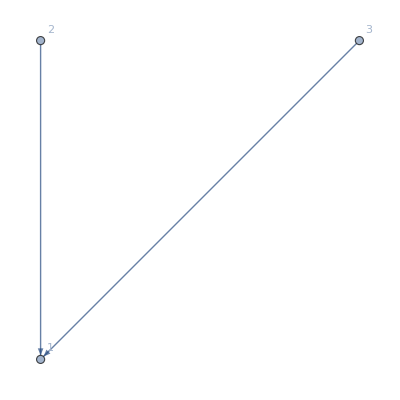
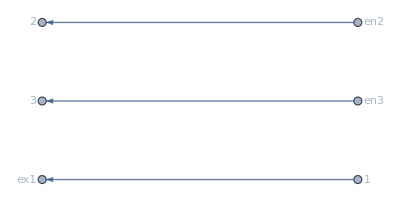
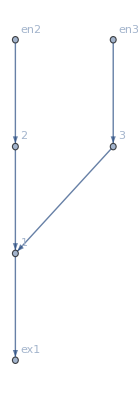
{0.037608,<|Vertices List→{1,2,3},Adjacency Matrix→{{0,0,0},{1,0,0},{1,0,0}},Entrance Vertices and Currents→{{2,10},{3,1}},Exit Vertices and Terminal Costs→{{1,0}},Switching Costs→{{2,1,3,27},{3,1,2,0}},VL→{1,2,3},AM→{{0,0,0},{1,0,0},{1,0,0}},EVC→{{2,10},{3,1}},EVTC→{{1,0}},SC→{{2,1,3,27},{3,1,2,0}},BG→-Graphics-,EntranceVertices→{2,3},InwardVertices→<|2→en2,3→en3|>,ExitVertices→{1},OutwardVertices→<|1→ex1|>,InEdges→{en2->2,en3->3},OutEdges→{1->ex1},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->ex1,2->1,3->1,en2->2,en3->3},BEL→{2->1,3->1},FVL→{1,2,3,en2,en3,ex1},jargs→{{1,1->ex1},{ex1,1->ex1},{2,2->1},{1,2->1},{3,3->1},{1,3->1},{en2,en2->2},{2,en2->2},{en3,en3->3},{3,en3->3}},uargs→{{1,1->ex1},{ex1,1->ex1},{2,2->1},{1,2->1},{3,3->1},{1,3->1},{en2,en2->2},{2,en2->2},{en3,en3->3},{3,en3->3}},AllTransitions→{{1,1->ex1,2->1},{1,1->ex1,3->1},{1,2->1,1->ex1},{1,2->1,3->1},{1,3->1,1->ex1},{1,3->1,2->1},{2,2->1,en2->2},{2,en2->2,2->1},{3,3->1,en3->3},{3,en3->3,3->1}},EntryArgs→{{2,en2->2},{3,en3->3}},EntryDataAssociation→<|{2,en2->2}→10,{3,en3->3}→1|>,ExitCosts→<|ex1→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10},jvars→<|{1,1->ex1}→j1,{ex1,1->ex1}→j2,{2,2->1}→j3,{1,2->1}→j4,{3,3->1}→j5,{1,3->1}→j6,{en2,en2->2}→j7,{2,en2->2}→j8,{en3,en3->3}→j9,{3,en3->3}→j10|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10},uvars→<|{1,1->ex1}→u1,{ex1,1->ex1}→u2,{2,2->1}→u3,{1,2->1}→u4,{3,3->1}→u5,{1,3->1}→u6,{en2,en2->2}→u7,{2,en2->2}→u8,{en3,en3->3}→u9,{3,en3->3}→u10|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10},jtvars→<|{1,1->ex1,2->1}→jt1,{1,1->ex1,3->1}→jt2,{1,2->1,1->ex1}→jt3,{1,2->1,3->1}→jt4,{1,3->1,1->ex1}→jt5,{1,3->1,2->1}→jt6,{2,2->1,en2->2}→jt7,{2,en2->2,2->1}→jt8,{3,3->1,en3->3}→jt9,{3,en3->3,3->1}→jt10|>,SignedCurrents→<|2->1→-j3+j4,3->1→-j5+j6|>,SwitchingCosts→<|{1,1->ex1,2->1}→1000000,{1,1->ex1,3->1}→1000000,{1,2->1,1->ex1}→0,{1,2->1,3->1}→27,{1,3->1,1->ex1}→0,{1,3->1,2->1}→0,{2,2->1,en2->2}→1000000,{2,en2->2,2->1}→0,{3,3->1,en3->3}→1000000,{3,en3->3,3->1}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0),EqTransitionCompCon→(jt1==0||jt3==0)&&(jt10==0||jt9==0)&&(jt2==0||jt5==0)&&(jt4==0||jt6==0)&&(jt7==0||jt8==0),NoDeadEnds→{{1,1->ex1},{1,2->1},{1,3->1},{2,2->1},{2,en2->2},{3,3->1},{3,en3->3}},EqBalanceSplittingCurrents→j1==jt1+jt2&&j4==jt3+jt4&&j6==jt5+jt6&&j3==jt7&&j8==jt8&&j5==jt9&&j10==jt10,BalanceSplittingCurrents→{j1-jt1-jt2,j4-jt3-jt4,j6-jt5-jt6,j3-jt7,j8-jt8,j5-jt9,j10-jt10},NoDeadStarts→{{ex1,1->ex1},{2,2->1},{3,3->1},{1,2->1},{en2,en2->2},{1,3->1},{en3,en3->3}},RuleBalanceGatheringCurrents→<|j2→jt3+jt5,j3→jt1+jt6,j5→jt2+jt4,j4→jt8,j7→jt7,j6→jt10,j9→jt9|>,BalanceGatheringCurrents→{-j2+jt3+jt5,-j3+jt1+jt6,-j5+jt2+jt4,-j4+jt8,-j7+jt7,-j6+jt10,-j9+jt9},EqBalanceGatheringCurrents→j2==jt3+jt5&&j3==jt1+jt6&&j5==jt2+jt4&&j4==jt8&&j7==jt7&&j6==jt10&&j9==jt9,EqEntryIn→{j8==10,j10==1},RuleEntryOut→<|j7→0,j9→0|>,RuleExitCurrentsIn→<|j1→0|>,RuleExitValues→<|u2→0|>,EqValueAuxiliaryEdges→u7==u8&&u9==u10&&u1==u2,OutRules→{{1,1->ex1,1->ex1}→∞,{1,1->ex1,2->1}→∞,{1,1->ex1,3->1}→∞,{1,1->ex1,en2->2}→∞,{1,1->ex1,en3->3}→∞},InRules→{{2,2->1,en2->2}→∞,{3,2->1,en3->3}→∞,{2,en2->2,en2->2}→∞,{3,en2->2,en3->3}→∞,{2,3->1,en2->2}→∞,{3,3->1,en3->3}→∞,{2,en3->3,en2->2}→∞,{3,en3->3,en3->3}→∞},EqSwitchingByVertex→{u1≤1000000+u4&&u1≤1000000+u6&&u4≤u1&&u4≤27+u6&&u6≤u1&&u6≤u4,u3≤1000000+u8&&u8≤u3,u5≤1000000+u10&&u10≤u5},EqCompCon→(jt1==0||1000000-u1+u4==0)&&(jt2==0||1000000-u1+u6==0)&&(jt3==0||u1-u4==0)&&(jt4==0||27-u4+u6==0)&&(jt5==0||u1-u6==0)&&(jt6==0||u4-u6==0)&&(jt7==0||1000000-u3+u8==0)&&(jt8==0||u3-u8==0)&&(jt9==0||1000000+u10-u5==0)&&(jt10==0||-u10+u5==0),Nlhs→{-j3+j4-u3+u4,-j5+j6-u5+u6},CostArgs→<|{1,1->ex1}→Identity,{ex1,1->ex1}→(0&),{2,2->1}→Identity,{1,2->1}→Identity,{3,3->1}→Identity,{1,3->1}→Identity,{en2,en2->2}→Identity,{2,en2->2}→(0&),{en3,en3->3}→Identity,{3,en3->3}→(0&),{1,1->ex1,2->1}→(10^4&),{1,1->ex1,3->1}→(10^4&),{1,2->1,1->ex1}→(1/10^4&),{1,2->1,3->1}→(1/10^4&),{1,3->1,1->ex1}→(1/10^4&),{1,3->1,2->1}→(1/10^4&),{2,2->1,en2->2}→(10^4&),{2,en2->2,2->1}→(1/10^4&),{3,3->1,en3->3}→(10^4&),{3,en3->3,3->1}→(1/10^4&)|>,Nrhs→{-j3+j4-IntM[-j3+j4,2->1],-j5+j6-IntM[-j5+j6,3->1]},costpluscurrents→<|cpc1→-j3+j4-IntM[-j3+j4,2->1],cpc2→-j5+j6-IntM[-j5+j6,3->1]|>,EqGeneral→-j3+j4-u3+u4==cpc1&&-j5+j6-u5+u6==cpc2,InitRules→<|j8→10,j10→1,j7→0,j9→0,j1→0,j2→11,j3→0,j5→0,j4→10,j6→1,u2→0,jt10→1,jt2→0,jt3→10,jt6→0,jt7→0,jt8→10,jt9→0,u1→0,u8→u3,u9→u10,jt1→0,jt4→0,jt5→1,u5→u10,u7→u3,u4→cpc1+j3-j4+u3,u6→cpc2+j5-j6+u5|>,NewSystem→{True,True,True},AssoCritical→<|j8→10,j10→1,j7→0,j9→0,j1→0,j2→11,j3→0,j5→0,j4→10,j6→1,u2→0,jt10→1,jt2→0,jt3→10,jt6→0,jt7→0,jt8→10,jt9→0,u1→0,u8→u3,u9→u10,jt1→0,jt4→0,jt5→1,u5→u10,u7→u3,u4→j3-j4+u3,u6→j5-j6+u5|>|>}

```mathematica
crit=CriticalCongestionSolver[d2e = Data2Equations[Data/.{I1->10,I2->1,U1->0,S1->27,S2->0}]]//AbsoluteTiming
```

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

EqEntryIn: j8==10&&j10==1	True

EqValueAuxiliaryEdges: u7==u8&&u9==u10&&u1==u2	True

EqCompCon: (jt1==0||1000000-u1+u4==0)&&(jt2==0||1000000-u1+u6==0)&&(jt3==0||u1-u4==0)&&(jt4==0||27-u4+u6==0)&&(jt5==0||u1-u6==0)&&(jt6==0||u4-u6==0)&&(jt7==0||1000000-u3+u8==0)&&(jt8==0||u3-u8==0)&&(jt9==0||1000000+u10-u5==0)&&(jt10==0||-u10+u5==0)	-j3+j4-u3==0&&-j5+j6-u5==0

EqBalanceSplittingCurrents: j1==jt1+jt2&&j4==jt3+jt4&&j6==jt5+jt6&&j3==jt7&&j8==jt8&&j5==jt9&&j10==jt10	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)	True

EqTransitionCompCon: (jt1==0||jt3==0)&&(jt10==0||jt9==0)&&(jt2==0||jt5==0)&&(jt4==0||jt6==0)&&(jt7==0||jt8==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0	True

EqSwitchingByVertex: u1≤1000000+u4&&u1≤1000000+u6&&u4≤u1&&u4≤27+u6&&u6≤u1&&u6≤u4&&u3≤1000000+u8&&u8≤u3&&u5≤1000000+u10&&u10≤u5	j4≤1000000+j3+u3&&j6≤1000000+j5+u5&&j3+u3≤j4&&j3+j6+u3≤27+j4+j5+u5&&j5+u5≤j6&&j4+j5+u5≤j3+j6+u3&&u3≤u3&&u10≤u10

Nlhs: {-j3+j4-u3+u4,-j5+j6-u5+u6}	{10.+j3-1. j4,1.+j5-1. j6-1. u10+u5}

Nrhs: {-j3+j4-IntM[-j3+j4,2->1],-j5+j6-IntM[-j5+j6,3->1]}	{-5.44452,0.0741253}

Max error for non-linear solution: Max[15.4445+j3-1. j4,0.925875+j5-1. j6-1. u10+u5]

<|j8→10,j10→1,j7→0,j9→0,j1→0,j2→11,j3→0,j5→0,j4→10,j6→1,u2→0,jt10→1,jt2→0,jt3→10,jt6→0,jt7→0,jt8→10,jt9→0,u1→0,u8→u3,u9→u10,jt1→0,jt4→0,jt5→1,u5→u10,u7→u3,u4→j3-j4+u3,u6→j5-j6+u5|>

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3},"Adjacency Matrix"->{{0,0,0},{1,0,0},{1,0,0}},"Entrance Vertices and Currents"->{{2,I1},{3,I2}},"Exit Vertices and Terminal Costs"->{{1,U1}},"Switching Costs"->{{2,1,3,S1},{3,1,2,S2}}|>;
```

```mathematica
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->10,I2->1,U1->0,S1->27,S2->0}]];)//AbsoluteTiming
```

{10-u3==0&&1-u10==0,True,True}

{0.053374,Null}

```mathematica
NS=And@@{1-u3==0&&1-u10==0,True,True};
Reduce[NS,Reals]//AbsoluteTiming
```

{0.000386,u3==1&&u10==1}

```mathematica
d2e
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,0,0},{1,0,0},{1,0,0}},Entrance Vertices and Currents→{{2,10},{3,1}},Exit Vertices and Terminal Costs→{{1,0}},Switching Costs→{{2,1,3,27},{3,1,2,0}},VL→{1,2,3},AM→{{0,0,0},{1,0,0},{1,0,0}},EVC→{{2,10},{3,1}},EVTC→{{1,0}},SC→{{2,1,3,27},{3,1,2,0}},BG→-Graphics-,EntranceVertices→{2,3},InwardVertices→<|2→en2,3→en3|>,ExitVertices→{1},OutwardVertices→<|1→ex1|>,InEdges→{en2->2,en3->3},OutEdges→{1->ex1},AuxiliaryGraph→-Graphics-,FG→-Graphics-,EL→{1->ex1,2->1,3->1,en2->2,en3->3},BEL→{2->1,3->1},FVL→{1,2,3,en2,en3,ex1},jargs→{{1,1->ex1},{ex1,1->ex1},{2,2->1},{1,2->1},{3,3->1},{1,3->1},{en2,en2->2},{2,en2->2},{en3,en3->3},{3,en3->3}},uargs→{{1,1->ex1},{ex1,1->ex1},{2,2->1},{1,2->1},{3,3->1},{1,3->1},{en2,en2->2},{2,en2->2},{en3,en3->3},{3,en3->3}},AllTransitions→{{1,1->ex1,2->1},{1,1->ex1,3->1},{1,2->1,1->ex1},{1,2->1,3->1},{1,3->1,1->ex1},{1,3->1,2->1},{2,2->1,en2->2},{2,en2->2,2->1},{3,3->1,en3->3},{3,en3->3,3->1}},EntryArgs→{{2,en2->2},{3,en3->3}},EntryDataAssociation→<|{2,en2->2}→10,{3,en3->3}→1|>,ExitCosts→<|ex1→0|>,js→{j1,j2,j3,j4,j5,j6,j7,j8,j9,j10},jvars→<|{1,1->ex1}→j1,{ex1,1->ex1}→j2,{2,2->1}→j3,{1,2->1}→j4,{3,3->1}→j5,{1,3->1}→j6,{en2,en2->2}→j7,{2,en2->2}→j8,{en3,en3->3}→j9,{3,en3->3}→j10|>,us→{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10},uvars→<|{1,1->ex1}→u1,{ex1,1->ex1}→u2,{2,2->1}→u3,{1,2->1}→u4,{3,3->1}→u5,{1,3->1}→u6,{en2,en2->2}→u7,{2,en2->2}→u8,{en3,en3->3}→u9,{3,en3->3}→u10|>,jts→{jt1,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jt10},jtvars→<|{1,1->ex1,2->1}→jt1,{1,1->ex1,3->1}→jt2,{1,2->1,1->ex1}→jt3,{1,2->1,3->1}→jt4,{1,3->1,1->ex1}→jt5,{1,3->1,2->1}→jt6,{2,2->1,en2->2}→jt7,{2,en2->2,2->1}→jt8,{3,3->1,en3->3}→jt9,{3,en3->3,3->1}→jt10|>,SignedCurrents→<|2->1→-j3+j4,3->1→-j5+j6|>,SwitchingCosts→<|{1,1->ex1,2->1}→1000,{1,1->ex1,3->1}→1000,{1,2->1,1->ex1}→0,{1,2->1,3->1}→27,{1,3->1,1->ex1}→0,{1,3->1,2->1}→0,{2,2->1,en2->2}→1000,{2,en2->2,2->1}→0,{3,3->1,en3->3}→1000,{3,en3->3,3->1}→0|>,EqPosJs→j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0,EqPosJts→jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0,EqCurrentCompCon→(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0),EqTransitionCompCon→(jt1==0||jt3==0)&&(jt10==0||jt9==0)&&(jt2==0||jt5==0)&&(jt4==0||jt6==0)&&(jt7==0||jt8==0),NoDeadEnds→{{1,1->ex1},{1,2->1},{1,3->1},{2,2->1},{2,en2->2},{3,3->1},{3,en3->3}},EqBalanceSplittingCurrents→j1==jt1+jt2&&j4==jt3+jt4&&j6==jt5+jt6&&j3==jt7&&j8==jt8&&j5==jt9&&j10==jt10,BalanceSplittingCurrents→{j1-jt1-jt2,j4-jt3-jt4,j6-jt5-jt6,j3-jt7,j8-jt8,j5-jt9,j10-jt10},NoDeadStarts→{{ex1,1->ex1},{2,2->1},{3,3->1},{1,2->1},{en2,en2->2},{1,3->1},{en3,en3->3}},RuleBalanceGatheringCurrents→<|j2→jt3+jt5,j3→jt1+jt6,j5→jt2+jt4,j4→jt8,j7→jt7,j6→jt10,j9→jt9|>,BalanceGatheringCurrents→{-j2+jt3+jt5,-j3+jt1+jt6,-j5+jt2+jt4,-j4+jt8,-j7+jt7,-j6+jt10,-j9+jt9},EqBalanceGatheringCurrents→j2==jt3+jt5&&j3==jt1+jt6&&j5==jt2+jt4&&j4==jt8&&j7==jt7&&j6==jt10&&j9==jt9,EqEntryIn→{j8==10,j10==1},RuleEntryOut→<|j7→0,j9→0|>,RuleExitCurrentsIn→<|j1→0|>,RuleExitValues→<|u2→0|>,EqValueAuxiliaryEdges→u7==u8&&u9==u10&&u1==u2,OutRules→{{1,1->ex1,1->ex1}→∞,{1,1->ex1,2->1}→∞,{1,1->ex1,3->1}→∞,{1,1->ex1,en2->2}→∞,{1,1->ex1,en3->3}→∞},InRules→{{2,2->1,en2->2}→∞,{3,2->1,en3->3}→∞,{2,en2->2,en2->2}→∞,{3,en2->2,en3->3}→∞,{2,3->1,en2->2}→∞,{3,3->1,en3->3}→∞,{2,en3->3,en2->2}→∞,{3,en3->3,en3->3}→∞},EqSwitchingByVertex→{u1≤1000+u4&&u1≤1000+u6&&u4≤u1&&u4≤27+u6&&u6≤u1&&u6≤u4,u3≤1000+u8&&u8≤u3,u5≤1000+u10&&u10≤u5},EqCompCon→(jt1==0||1000-u1+u4==0)&&(jt2==0||1000-u1+u6==0)&&(jt3==0||u1-u4==0)&&(jt4==0||27-u4+u6==0)&&(jt5==0||u1-u6==0)&&(jt6==0||u4-u6==0)&&(jt7==0||1000-u3+u8==0)&&(jt8==0||u3-u8==0)&&(jt9==0||1000+u10-u5==0)&&(jt10==0||-u10+u5==0),Nlhs→{-j3+j4-u3+u4,-j5+j6-u5+u6},CostArgs→<|{1,1->ex1}→Identity,{ex1,1->ex1}→(0&),{2,2->1}→Identity,{1,2->1}→Identity,{3,3->1}→Identity,{1,3->1}→Identity,{en2,en2->2}→Identity,{2,en2->2}→(0&),{en3,en3->3}→Identity,{3,en3->3}→(0&),{1,1->ex1,2->1}→(10^2&),{1,1->ex1,3->1}→(10^2&),{1,2->1,1->ex1}→(1/10^2&),{1,2->1,3->1}→(1/10^2&),{1,3->1,1->ex1}→(1/10^2&),{1,3->1,2->1}→(1/10^2&),{2,2->1,en2->2}→(10^2&),{2,en2->2,2->1}→(1/10^2&),{3,3->1,en3->3}→(10^2&),{3,en3->3,3->1}→(1/10^2&)|>,Nrhs→{-j3+j4-IntM[-j3+j4,2->1],-j5+j6-IntM[-j5+j6,3->1]}|>

```mathematica
MFGEquations["uvars"]
```

<|{1,1->ex6175}→u6196,{2,2->1}→u6197,{3,3->1}→u6198,{en6173,en6173->2}→u6199,{en6174,en6174->3}→u6200,{ex6175,1->ex6175}→u6201,{1,2->1}→u6202,{1,3->1}→u6203,{2,en6173->2}→u6204,{3,en6174->3}→u6205|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
True
and the rules are:
<|j6179→1,j6180→1,u6201→0,j6176→2,j6177→1,j6178→1,j6181→0,j6182→0,j6183→0,j6184→0,j6185→0,jt6186→0,jt6187→0,jt6188→1,jt6189→0,jt6190→1,jt6191→0,jt6192→0,jt6193→1,jt6194→0,jt6195→1,u6196→0,u6202→-1+1,u6203→-1+1,u6204→1,u6205→1,u6197→1,u6198→1,u6199→1,u6200→1|>

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.011752,Null}

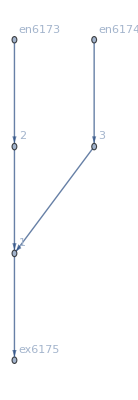

<|j6176→2,j6177→1,j6178→1,j6179→1,j6180→1,j6181→0,j6182→0,j6183→0,j6184→0,j6185→0,jt6186→0,jt6187→0,jt6188→1,jt6189→0,jt6190→1,jt6191→0,jt6192→0,jt6193→1,jt6194→0,jt6195→1,u6196→0,u6197→1,u6198→1,u6199→1,u6200→1,u6201→0,u6202→0,u6203→0,u6204→1,u6205→1|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,I2->1,U1->0,S1->27,S2->0}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20736×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20736×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→17.582,u2797→17.2347,u2798→17.582,u2799→17.2347,u2800→15.,u2801→15.,u2802→15.,u2803→17.582,u2804→17.2347|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.35529×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.35529×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→18.1613,u2797→17.6164,u2798→18.1613,u2799→17.6164,u2800→15.,u2801→15.,u2802→15.,u2803→18.1613,u2804→17.6164|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.07112×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.07112×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→20.0239,u2797→18.7439,u2798→20.0239,u2799→18.7439,u2800→15.,u2801→15.,u2802→15.,u2803→20.0239,u2804→18.7439|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.72121×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.72121×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→59.966,u2797→34.5967,u2798→59.966,u2799→34.5967,u2800→15.,u2801→15.,u2802→15.,u2803→59.966,u2804→34.5967|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[9.10632×10^-14,ComplexInfinity]

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→95.,u2797→45.,u2798→95.,u2799→45.,u2800→15.,u2801→15.,u2802→15.,u2803→95.,u2804→45.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→378.906,u2797→105.546,u2798→378.906,u2799→105.546,u2800→15.,u2801→15.,u2802→15.,u2803→378.906,u2804→105.546|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→290058.,u2797→9741.29,u2798→290058.,u2799→9741.29,u2800→15.,u2801→15.,u2802→15.,u2803→290058.,u2804→9741.29|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→5.6037×10^18,u2797→2.32106×10^12,u2798→5.6037×10^18,u2799→2.32106×10^12,u2800→15.,u2801→15.,u2802→15.,u2803→5.6037×10^18,u2804→2.32106×10^12|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→2.2049×10^106,u2797→8.26837×10^105,u2798→2.2049×10^106,u2799→8.26837×10^105,u2800→15.,u2801→15.,u2802→15.,u2803→2.2049×10^106,u2804→8.26837×10^105|>

```mathematica
(c->b)[[2]]
```

b

$Aborted

Lookup::invrl: The argument nn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

EqEntryIn: nn&&EqEntryIn&&$Failed	nn&&EqEntryIn&&$Failed/.nn[AssoNonCritical]

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

EqValueAuxiliaryEdges: Lookup[nn,EqValueAuxiliaryEdges,$Failed]	Lookup[nn,EqValueAuxiliaryEdges,$Failed]/.nn[AssoNonCritical]

ReplaceAll::reps: {nn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

EqCompCon: Lookup[nn,EqCompCon,$Failed]	Lookup[nn,EqCompCon,$Failed]/.nn[AssoNonCritical]

EqBalanceSplittingCurrents: Lookup[nn,EqBalanceSplittingCurrents,$Failed]	Lookup[nn,EqBalanceSplittingCurrents,$Failed]/.nn[AssoNonCritical]

EqCurrentCompCon: Lookup[nn,EqCurrentCompCon,$Failed]	Lookup[nn,EqCurrentCompCon,$Failed]/.nn[AssoNonCritical]

EqTransitionCompCon: Lookup[nn,EqTransitionCompCon,$Failed]	Lookup[nn,EqTransitionCompCon,$Failed]/.nn[AssoNonCritical]

EqPosJs: Lookup[nn,EqPosJs,$Failed]	Lookup[nn,EqPosJs,$Failed]/.nn[AssoNonCritical]

EqPosJts: Lookup[nn,EqPosJts,$Failed]	Lookup[nn,EqPosJts,$Failed]/.nn[AssoNonCritical]

EqSwitchingByVertex: nn&&EqSwitchingByVertex&&$Failed	nn&&EqSwitchingByVertex&&$Failed/.nn[AssoNonCritical]

Nlhs: Lookup[nn,Nlhs,$Failed]	Lookup[nn,Nlhs,$Failed]/.nn[AssoNonCritical]

Nrhs: Lookup[nn,Nrhs,$Failed]	Lookup[nn,Nrhs,$Failed]/.nn[AssoNonCritical]

Max error for non-linear solution: (Lookup[nn,Nlhs,$Failed]/.nn[AssoNonCritical])-(Lookup[nn,Nrhs,$Failed]/.nn[AssoNonCritical])